```mathematica
(* source: 2006 UN Food and Agriculture *)
horsePop  ={{"United States", 321450000, 9500000},{"China", 1371060000, 7000000},
{"Mexico", 121005815, 6260000},
{"Brazil", 204633000, 5787249},
{"Argentina", 43131966, 3655000},
{"Colombia", 48224500, 2533621},
{"Mongolia", 3027126, 2029100},
{"Ethiopia", 90076012, 1655383},
{"Russian Federation", 146524812, 1319358},
{"Kazakhstan", 17519000, 1163500}}
```

{{United States,321450000,9500000},{China,1371060000,7000000},{Mexico,121005815,6260000},{Brazil,204633000,5787249},{Argentina,43131966,3655000},{Colombia,48224500,2533621},{Mongolia,3027126,2029100},{Ethiopia,90076012,1655383},{Russian Federation,146524812,1319358},{Kazakhstan,17519000,1163500}}

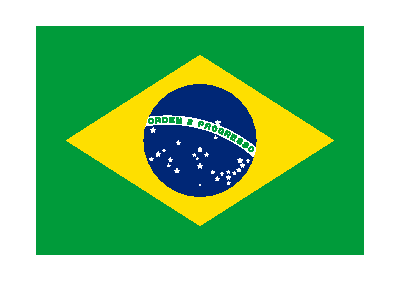



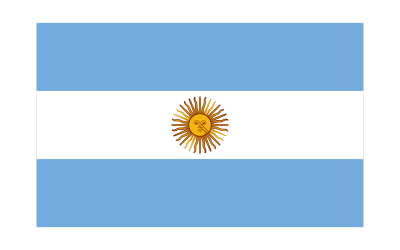
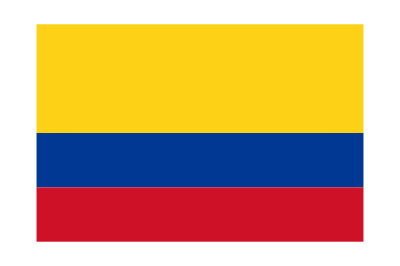
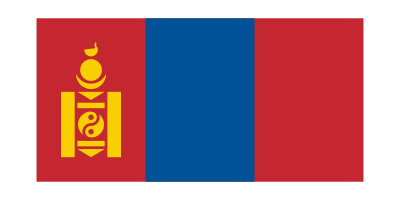
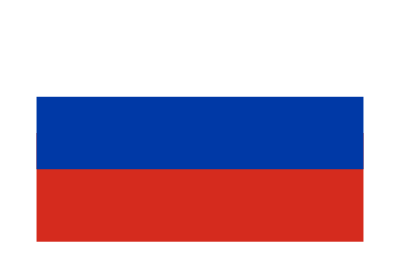
{{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07},{-Graphics-,0.07}}

```mathematica
Framed[{CountryData[horsePop[[4,1]], "Flag"]},  FrameMargins->0,ContentPadding->False,Background->Black]
allFlags = Table[{Graphics[CountryData[horsePop[[i, 1]], "Flag"]], .07}, {i, 1, Length[horsePop]}]
```

```mathematica
listHorsePop = Drop[horsePop, None,1]
partitionedHorses = Partition[Drop[horsePop, None, 1],1]
Partition[Flatten[listHorsePop],2]
```

{{321450000,9500000},{1371060000,7000000},{121005815,6260000},{204633000,5787249},{43131966,3655000},{48224500,2533621},{3027126,2029100},{90076012,1655383},{146524812,1319358},{17519000,1163500}}

{{{321450000,9500000}},{{1371060000,7000000}},{{121005815,6260000}},{{204633000,5787249}},{{43131966,3655000}},{{48224500,2533621}},{{3027126,2029100}},{{90076012,1655383}},{{146524812,1319358}},{{17519000,1163500}}}

{{321450000,9500000},{1371060000,7000000},{121005815,6260000},{204633000,5787249},{43131966,3655000},{48224500,2533621},{3027126,2029100},{90076012,1655383},{146524812,1319358},{17519000,1163500}}

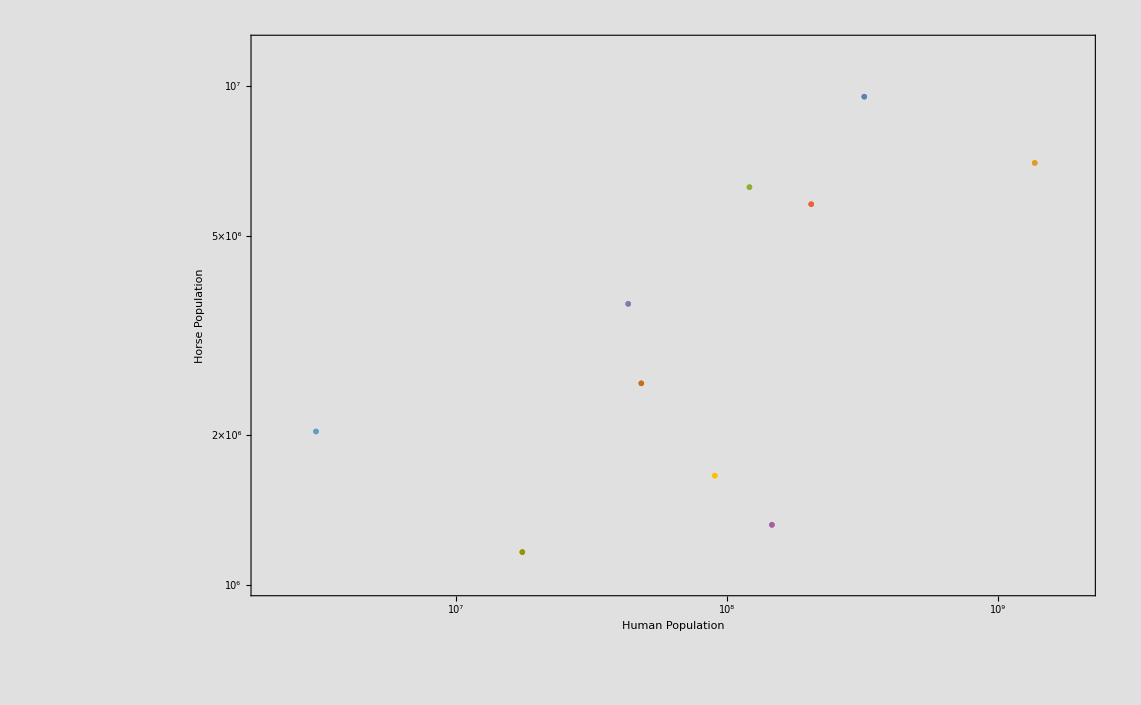

```mathematica
ListLogLogPlot[partitionedHorses, PlotRange->{{2000000, 2000000000},{1000000, 12000000}}, PlotMarkers->allFlags, Axes->False,Frame->True,Background->RGBColor[0.88, 0.88, 0.88], FrameLabel->{"Human Population","Horse Population"}, PlotMarkers->{{allFlags}},  BaseStyle->{FontFamily->"Helvetica Neue",FontSize->16}]
```

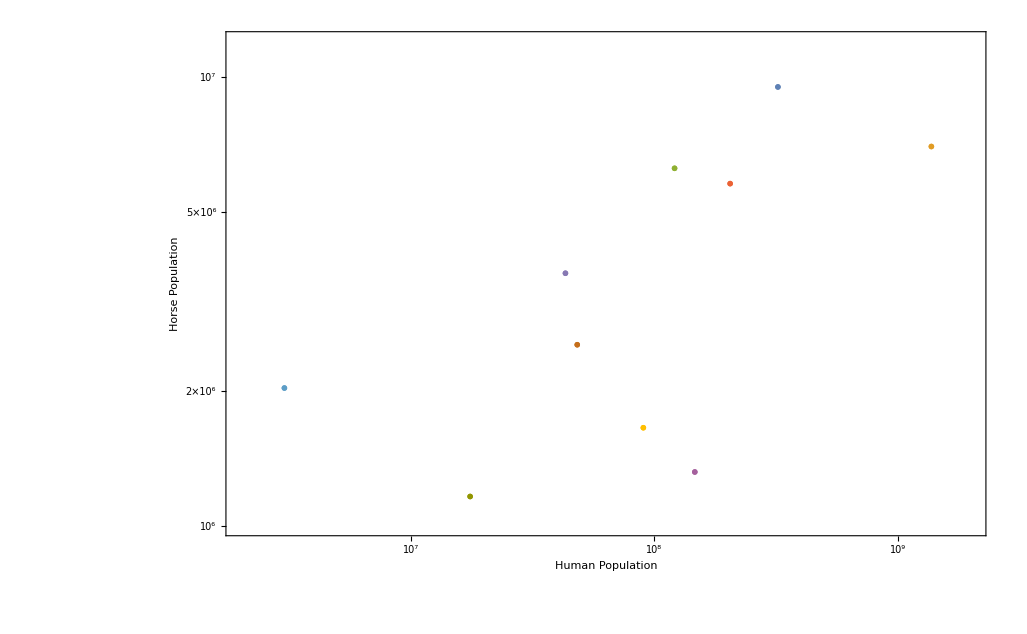

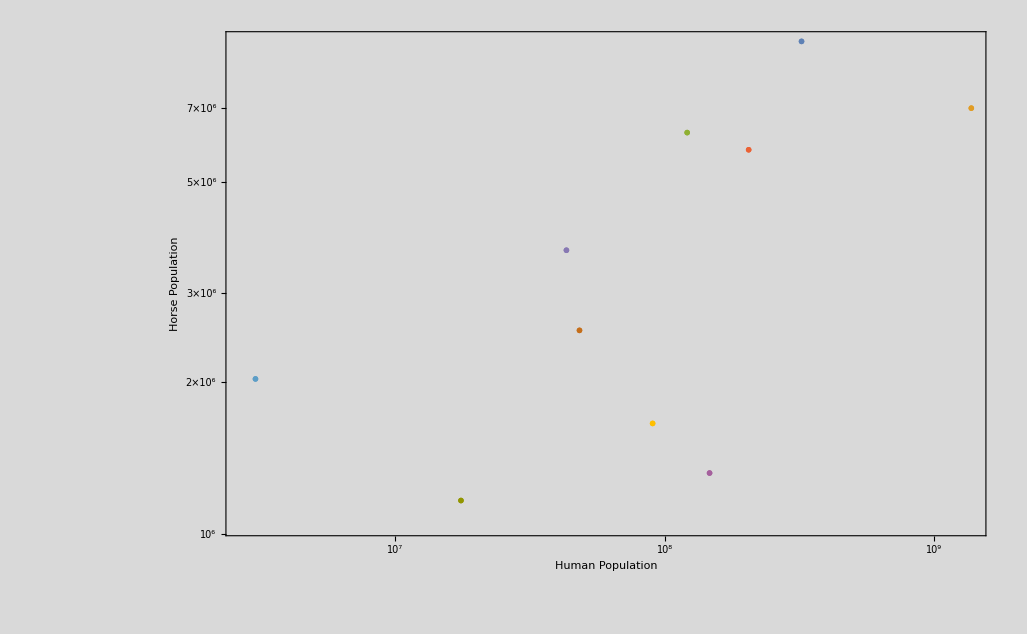

```mathematica
Show[%429,Background->LightGray]
```

```mathematica
s
```

```mathematica
Length[allFlags]
Length[horsePop]
```

10

10

```mathematica
allFlags
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

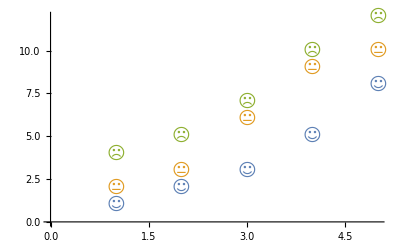

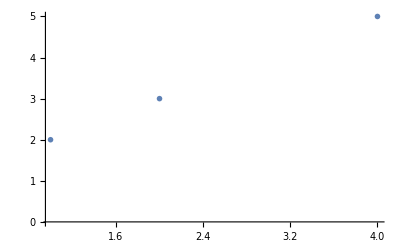

```mathematica
ListPlot[{{1,2,3,5,8},{2,3,6,9,10},{4,5,7,10,12}},PlotMarkers->{"☺","😐","☹"}]
ListPlot[{{1,2},{2,3},{4,5}},PlotMarkers->allFlags]
```